```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

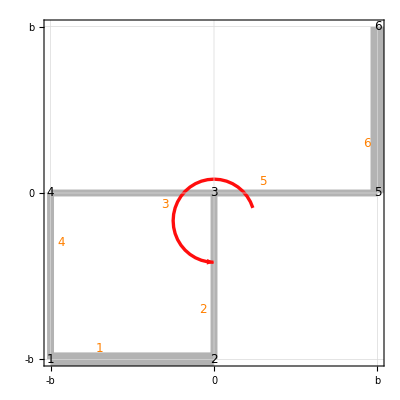

```mathematica
example={$$nodes->{{-b, -b}, {0, -b}, {0, 0}, {-b, 0}, {b, 0}, {b, b}},
$$edges->{{1, 2}, {2, 3}, {3, 4}, {4, 1}, {3, 5}, {5, 6}},
$$thicknesses->{2s,s,s,s,s,2s},$$absname->t,$$thname->z,
$$traction->0,$$wheretraction->{0, 0},
$$shear->{0, 0}, $$whereshear->{0, 0},
$$bending->{0, 0}, $$torsion->M}; dSVtShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{b→0.75,M→0.94,s→0.08}

Edge lengths

{{b,b,b,b,b,b}}

Edges areas Ai

{{2 b s,b s,b s,b s,b s,2 b s}}

Total area A

8 b s

Edges static moments sPi

{{{-b^2 s,-2 b^2 s},{0,-(b^2 s)/2},{-(b^2 s)/2,0},{-b^2 s,-(b^2 s)/2},{(b^2 s)/2,0},{2 b^2 s,b^2 s}}}

Static moment sP

{{0,-2 b^2 s}}

Edge centroids Gi

{{{-b/2,-b},{0,-b/2},{-b/2,0},{-b,-b/2},{b/2,0},{b,b/2}}}

Centroid G

{{0,-b/4}}

Edges Euler inertia tensors IPi

{{{{(2 b^3 s)/3,b^3 s},{b^3 s,2 b^3 s}},{{0,0},{0,(b^3 s)/3}},{{(b^3 s)/3,0},{0,0}},{{b^3 s,(b^3 s)/2},{(b^3 s)/2,(b^3 s)/3}},{{(b^3 s)/3,0},{0,0}},{{2 b^3 s,b^3 s},{b^3 s,(2 b^3 s)/3}}}}

Total Euler inertia tensor IP

{{(13 b^3 s)/3,(5 b^3 s)/2},{(5 b^3 s)/2,(10 b^3 s)/3}}

Inertia tensor after translation in the centroid IG

{{(13 b^3 s)/3,(5 b^3 s)/2},{(5 b^3 s)/2,(17 b^3 s)/6}}

Principal inertia momoments (jI, jII) and associated directions

{{1/12 (43-3 √109) b^3 s,{1/10 (3+√109),1}},{1/12 (43+3 √109) b^3 s,{1/10 (3-√109),1}}}

Rotation to principal directions

36.7

Radii of gyration (ρI, ρII)

{{1/4 √(1/6 (43-3 √109)) b,1/4 √(1/6 (43+3 √109)) b}}

Section moduli (WI, WII) and associated directions

{{{-(5 (-43+3 √109) b^2 s)/(63+6 √109),-(5 (-43+3 √109) b^2 s)/(93+6 √109)},{1/10 (3+√109),1}},{{1/9 (43+3 √109) b^2 s,(5 (43+3 √109) b^2 s)/(-3+6 √109)},{1/10 (3-√109),1}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{0,0,0}

Sigma in principal axis (ξ,η)

0

Neutral axis for sigma

{}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

89 b^2+90 b x1+360 x1 x2==204 x1^2+156 x2 (b+2 x2)

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-(13 b)/24,-(9 b)/16},{-b/18,-(37 b)/72},{(13 b)/24,b/16},{(5 b)/12,(2 b)/9},{-(11 b)/36,-(7 b)/36}}

(Shear) Cycles in terms of nodes

{{4,1,2,3,4}}

(Shear) Cycles in terms of edges

{{4,1,2,3}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-b,-b},{0,-b},{0,0},{-b,0},{b,0},{b,b},{-b,0}},{{1,2},{2,3},{3,4},{7,1},{3,5},{5,6}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0,0}

Cycles connectivity

{{1},{1},{1},{1},{0},{0}}

Congruence for statically undetermined shear, matrix ηij

{{(7 b)/(2 s)}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0,0}

Shear stiffness matrix

{{2279390/6543579,-21775/4362386},{-21775/4362386,1971860/6543579}}

Shear flexibility matrix

{{4732464/1648115,15678/329623},{15678/329623,5470536/1648115}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{-(829 b)/3038,-(2993 b)/6076}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{4,1,2,3}}

(Torsion) Cycles in terms of edges

{{4,1,2,3}}

Statically undetermined torsion, congruence matrix ηij

{{(7 b)/(2 s)}}

Statically undetermined torsion, vector  2Ω

{2 b^2}

Solution of the statically undetermined torsion

{(4 b s)/7}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{(2 M)/(8 b^2 s+21 s^3),(4 M)/(8 b^2 s+21 s^3),(4 M)/(8 b^2 s+21 s^3),(4 M)/(8 b^2 s+21 s^3),-(14 M z)/(8 b^3+21 b s^2),-(28 M z)/(8 b^3+21 b s^2)}}

Torsional inertias Jti

{{{4,1,2,3},(8 b^3 s)/7},{5,(b s^3)/3},{6,(8 b s^3)/3}}

Torsional inertia Jt

(8 b^3 s)/7+3 b s^3

-Graphics-

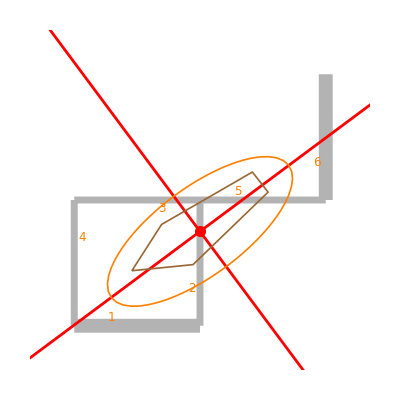

-Graphics-

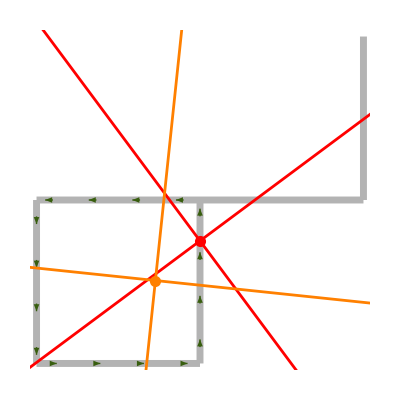

-Graphics-

-Graphics-

```mathematica
Last[sol]
```

{{assums Assunzioni numeriche,Numerical assumptions for visualization purposes,{b→0.75,M→0.94,s→0.08}},{edgelengths Lunghezze dei rami,Edge lengths,{{b,b,b,b,b,b}}},{edgeareas Aree dei rami,Edges areas Ai,{{2 b s,b s,b s,b s,b s,2 b s}}},{totalarea Area totale,Total area A,8 b s},{edgestaticmom Momenti statici dei rami,Edges static moments sPi,{{{-b^2 s,-2 b^2 s},{0,-(b^2 s)/2},{-(b^2 s)/2,0},{-b^2 s,-(b^2 s)/2},{(b^2 s)/2,0},{2 b^2 s,b^2 s}}}},{totalstaticmom Momento statico totale,Static moment sP,{{0,-2 b^2 s}}},{edgemasscenters Baricentri dei rami,Edge centroids Gi,{{{-b/2,-b},{0,-b/2},{-b/2,0},{-b,-b/2},{b/2,0},{b,b/2}}}},{totalmasscenter Baricentro,Centroid G,{{0,-b/4}}},{edgeinertias Momenti d'inerzia dei rami,Edges Euler inertia tensors IPi,{{{{(2 b^3 s)/3,b^3 s},{b^3 s,2 b^3 s}},{{0,0},{0,(b^3 s)/3}},{{(b^3 s)/3,0},{0,0}},{{b^3 s,(b^3 s)/2},{(b^3 s)/2,(b^3 s)/3}},{{(b^3 s)/3,0},{0,0}},{{2 b^3 s,b^3 s},{b^3 s,(2 b^3 s)/3}}}}},{totalinertia Momento d'inerzia totale,Total Euler inertia tensor IP,{{(13 b^3 s)/3,(5 b^3 s)/2},{(5 b^3 s)/2,(10 b^3 s)/3}}},{masscenterinertia Momento d'inerzia dopo translazione nel baricentro,Inertia tensor after translation in the centroid IG,{{(13 b^3 s)/3,(5 b^3 s)/2},{(5 b^3 s)/2,(17 b^3 s)/6}}},{inertiaprinc Momenti e direzioni d'inerzia principali,Principal inertia momoments (jI, jII) and associated directions,{{1/12 (43-3 √109) b^3 s,{1/10 (3+√109),1}},{1/12 (43+3 √109) b^3 s,{1/10 (3-√109),1}}}},{rotazprinc Rotazione per assi principali d'inerzia,Rotation to principal directions,36.7},{inertiarot rotatori d'inerzia,Radii of gyration (ρI, ρII),{{1/4 √(1/6 (43-3 √109)) b,1/4 √(1/6 (43+3 √109)) b}}},{sectionmoduli Moduli resistenza a flessione,Section moduli (WI, WII) and associated directions,{{{-(5 (-43+3 √109) b^2 s)/(63+6 √109),-(5 (-43+3 √109) b^2 s)/(93+6 √109)},{1/10 (3+√109),1}},{{1/9 (43+3 √109) b^2 s,(5 (43+3 √109) b^2 s)/(-3+6 √109)},{1/10 (3-√109),1}}}},{sigmacoeff Coefficienti {a0,a1,a2} di sigma,Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2),{0,0,0}},{sigmaprinc Sigma in assi principali,Sigma in principal axis (ξ,η),0},{neutralaxis Asse neutro sigma,Neutral axis for sigma,{}},{sigma0intprinc Intercette asse neutro con assi principali,Intersections of neutral axis with principal axis,{Last[{}],Last[{}]}},{iellipse Ellisse d'inerzia ,Inertia ellipse equation,89 b^2+90 b x1+360 x1 x2==204 x1^2+156 x2 (b+2 x2)},{inertiakernel Nocciolo d'inerzia,Kern (Convex hull (convex hull has been computed on a numerical instance!),{{-(13 b)/24,-(9 b)/16},{-b/18,-(37 b)/72},{(13 b)/24,b/16},{(5 b)/12,(2 b)/9},{-(11 b)/36,-(7 b)/36}}},{shearcyclesn Cicli,(Shear) Cycles in terms of nodes,{{4,1,2,3,4}}},{shearcyclese Cicli,(Shear) Cycles in terms of edges,{{4,1,2,3}}},{opengraph  Sezione principale aperta (problema iperstatico del taglio),Associated open graph {nodes, edges} (statically undetermined shear),{{{-b,-b},{0,-b},{0,0},{-b,0},{b,0},{b,b},{-b,0}},{{1,2},{2,3},{3,4},{7,1},{3,5},{5,6}}}},{opengraphtension Tensione su sezione aperta (problema iperstatico del taglio),Jourawsky shear on the associated open graph (statically undetermined shear),{0,0,0,0,0,0}},{cyclesconnectivity Connettivita dei cicli,Cycles connectivity ,{{1},{1},{1},{1},{0},{0}}},{shearcongruencematrix Matrice congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, matrix ηij ,{{(7 b)/(2 s)}}},{shearcongruencevector Termine noto congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, vector η0i,{0}},{shearcongruencesol soluzione congruenza (problema iperstatico di taglio),Statically undetermined shear solution: Prandtl function values,{0}},{taucongruencesol Soluzione congruenza (problema iperstatico del taglio),Statically undetermined shear solution: shear fluxes,{0,0,0,0,0,0}},{jourawskytau Tensione tangenziale dovuta al taglio nel centro di taglio (Jourawsky),Shear stress if the shear force is placed in the shear center,{0,0,0,0,0,0}},{shearfactors Fattori di rigidezza al taglio,Shear stiffness matrix,{{2279390/6543579,-21775/4362386},{-21775/4362386,1971860/6543579}}},{shearfactorsinv Fattori di flessibilita al taglio,Shear flexibility matrix,{{4732464/1648115,15678/329623},{15678/329623,5470536/1648115}}},{edgeshearresultants Risultanti taglio sui rami,Shear resultants on edges,{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}},{shearresultant Risultante del taglio,Shear resultant,{0,0}},{shearcenter Centro di taglio,Shear center,{{-(829 b)/3038,-(2993 b)/6076}}},{additionaltorque Momento torcente aggiuntivo,Additional torque due to eccentricity,0},{torsioncyclesn Base di cicli in termini di nodi,(Torsion) Cycles in terms of nodes,{{4,1,2,3}}},{torsioncyclesr Base di cicli in termini di rami,(Torsion) Cycles in terms of edges,{{4,1,2,3}}},{torsioncongruencematrix Matrice congruenza (problema iperstatico di torsione),Statically undetermined torsion, congruence matrix ηij,{{(7 b)/(2 s)}}},{torsioncongruencevector Termine noto congruenza (problema iperstatico di torsione),Statically undetermined torsion, vector  2Ω,{2 b^2}},{torsioncongruencesol soluzione congruenza (problema iperstatico di torsione),Solution of the statically undetermined torsion,{(4 b s)/7}},{torsionpartition ripartizione torsione sui cicli ,Torsion partition over the cycles  Ji/J,{1}},{torsionaltau Tensione tangenziale dovuta alla torsione,Shear stress due to torsion,{{(2 M)/(8 b^2 s+21 s^3),(4 M)/(8 b^2 s+21 s^3),(4 M)/(8 b^2 s+21 s^3),(4 M)/(8 b^2 s+21 s^3),-(14 M z)/(8 b^3+21 b s^2),-(28 M z)/(8 b^3+21 b s^2)}}},{torsionalstiffnesses Singole rigidezze inerzie torsionali (rami, rig),Torsional inertias Jti,{{{4,1,2,3},(8 b^3 s)/7},{5,(b s^3)/3},{6,(8 b s^3)/3}}},{torsionalstiffness Rigidezza Inerzia torsionale,Torsional inertia Jt,(8 b^3 s)/7+3 b s^3}}

```mathematica
valori1={b->Quantity[10,"Centimeters"],s->Quantity[0.5,"Centimeters"],z->Quantity[0.5,"Centimeters"],M->Quantity[10,"Kilonewtons*Centimeters"],G->Quantity[80,"Gigapascals"],z->s/2};
```

Quantity::timeout: A network operation for Quantity timed out. Please try again later.

Quantity::unkunit: Unable to interpret unit specification Kilonewtons*Centimeters.

```mathematica
Last[sol]/.valori1//N
```

{{assums Assunzioni numeriche,Numerical assumptions for visualization purposes,{10. cm→0.75,10. cm kN→0.94,0.5 cm→0.08}},{edgelengths Lunghezze dei rami,Edge lengths,{{10. cm,10. cm,10. cm,10. cm,10. cm,10. cm}}},{edgeareas Aree dei rami,Edges areas Ai,{{10. cm^2,5. cm^2,5. cm^2,5. cm^2,5. cm^2,10. cm^2}}},{totalarea Area totale,Total area A,40. cm^2},{edgestaticmom Momenti statici dei rami,Edges static moments sPi,{{{-50. cm^3,-100. cm^3},{0.,-25. cm^3},{-25. cm^3,0.},{-50. cm^3,-25. cm^3},{25. cm^3,0.},{100. cm^3,50. cm^3}}}},{totalstaticmom Momento statico totale,Static moment sP,{{0.,-100. cm^3}}},{edgemasscenters Baricentri dei rami,Edge centroids Gi,{{{-5. cm,-10. cm},{0.,-5. cm},{-5. cm,0.},{-10. cm,-5. cm},{5. cm,0.},{10. cm,5. cm}}}},{totalmasscenter Baricentro,Centroid G,{{0.,-2.5 cm}}},{edgeinertias Momenti d'inerzia dei rami,Edges Euler inertia tensors IPi,{{{{333.333 cm^4,500. cm^4},{500. cm^4,1000. cm^4}},{{0.,0.},{0.,166.667 cm^4}},{{166.667 cm^4,0.},{0.,0.}},{{500. cm^4,250. cm^4},{250. cm^4,166.667 cm^4}},{{166.667 cm^4,0.},{0.,0.}},{{1000. cm^4,500. cm^4},{500. cm^4,333.333 cm^4}}}}},{totalinertia Momento d'inerzia totale,Total Euler inertia tensor IP,{{2166.67 cm^4,1250. cm^4},{1250. cm^4,1666.67 cm^4}}},{masscenterinertia Momento d'inerzia dopo translazione nel baricentro,Inertia tensor after translation in the centroid IG,{{2166.67 cm^4,1250. cm^4},{1250. cm^4,1416.67 cm^4}}},{inertiaprinc Momenti e direzioni d'inerzia principali,Principal inertia momoments (jI, jII) and associated directions,{{486.628 cm^4,{1.34403,1.}},{3096.7 cm^4,{-0.744031,1.}}}},{rotazprinc Rotazione per assi principali d'inerzia,Rotation to principal directions,36.7},{inertiarot rotatori d'inerzia,Radii of gyration (ρI, ρII),{{3.48794 cm,8.79873 cm}}},{sectionmoduli Moduli resistenza a flessione,Section moduli (WI, WII) and associated directions,{{{23.2388 cm^3,18.7595 cm^3},{1.34403,1.}},{{412.894 cm^3,311.53 cm^3},{-0.744031,1.}}}},{sigmacoeff Coefficienti {a0,a1,a2} di sigma,Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2),{0.,0.,0.}},{sigmaprinc Sigma in assi principali,Sigma in principal axis (ξ,η),0.},{neutralaxis Asse neutro sigma,Neutral axis for sigma,{}},{sigma0intprinc Intercette asse neutro con assi principali,Intersections of neutral axis with principal axis,{Last[{}],Last[{}]}},{iellipse Ellisse d'inerzia ,Inertia ellipse equation,360. x1 x2+x1 (900. cm)+8900. cm^2==204. x1^2+156. x2 (2. x2+10. cm)},{inertiakernel Nocciolo d'inerzia,Kern (Convex hull (convex hull has been computed on a numerical instance!),{{-5.41667 cm,-5.625 cm},{-0.555556 cm,-5.13889 cm},{5.41667 cm,0.625 cm},{4.16667 cm,2.22222 cm},{-3.05556 cm,-1.94444 cm}}},{shearcyclesn Cicli,(Shear) Cycles in terms of nodes,{{4.,1.,2.,3.,4.}}},{shearcyclese Cicli,(Shear) Cycles in terms of edges,{{4.,1.,2.,3.}}},{opengraph  Sezione principale aperta (problema iperstatico del taglio),Associated open graph {nodes, edges} (statically undetermined shear),{{{-10. cm,-10. cm},{0.,-10. cm},{0.,0.},{-10. cm,0.},{10. cm,0.},{10. cm,10. cm},{-10. cm,0.}},{{1.,2.},{2.,3.},{3.,4.},{7.,1.},{3.,5.},{5.,6.}}}},{opengraphtension Tensione su sezione aperta (problema iperstatico del taglio),Jourawsky shear on the associated open graph (statically undetermined shear),{0.,0.,0.,0.,0.,0.}},{cyclesconnectivity Connettivita dei cicli,Cycles connectivity ,{{1.},{1.},{1.},{1.},{0.},{0.}}},{shearcongruencematrix Matrice congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, matrix ηij ,{{70.}}},{shearcongruencevector Termine noto congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, vector η0i,{0.}},{shearcongruencesol soluzione congruenza (problema iperstatico di taglio),Statically undetermined shear solution: Prandtl function values,{0.}},{taucongruencesol Soluzione congruenza (problema iperstatico del taglio),Statically undetermined shear solution: shear fluxes,{0.,0.,0.,0.,0.,0.}},{jourawskytau Tensione tangenziale dovuta al taglio nel centro di taglio (Jourawsky),Shear stress if the shear force is placed in the shear center,{0.,0.,0.,0.,0.,0.}},{shearfactors Fattori di rigidezza al taglio,Shear stiffness matrix,{{0.34834,-0.00499153},{-0.00499153,0.301343}}},{shearfactorsinv Fattori di flessibilita al taglio,Shear flexibility matrix,{{2.87144,0.0475634},{0.0475634,3.31927}}},{edgeshearresultants Risultanti taglio sui rami,Shear resultants on edges,{{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}},{shearresultant Risultante del taglio,Shear resultant,{0.,0.}},{shearcenter Centro di taglio,Shear center,{{-2.72877 cm,-4.92594 cm}}},{additionaltorque Momento torcente aggiuntivo,Additional torque due to eccentricity,0.},{torsioncyclesn Base di cicli in termini di nodi,(Torsion) Cycles in terms of nodes,{{4.,1.,2.,3.}}},{torsioncyclesr Base di cicli in termini di rami,(Torsion) Cycles in terms of edges,{{4.,1.,2.,3.}}},{torsioncongruencematrix Matrice congruenza (problema iperstatico di torsione),Statically undetermined torsion, congruence matrix ηij,{{70.}}},{torsioncongruencevector Termine noto congruenza (problema iperstatico di torsione),Statically undetermined torsion, vector  2Ω,{200. cm^2}},{torsioncongruencesol soluzione congruenza (problema iperstatico di torsione),Solution of the statically undetermined torsion,{2.85714 cm^2}},{torsionpartition ripartizione torsione sui cicli ,Torsion partition over the cycles  Ji/J,{1.}},{torsionaltau Tensione tangenziale dovuta alla torsione,Shear stress due to torsion,{{0.049674 kN/cm^2,0.099348 kN/cm^2,0.099348 kN/cm^2,0.099348 kN/cm^2,s (-0.00869295 kN/cm^2),s (-0.0173859 kN/cm^2)}}},{torsionalstiffnesses Singole rigidezze inerzie torsionali (rami, rig),Torsional inertias Jti,{{{4.,1.,2.,3.},571.429 cm^4},{5.,0.416667 cm^4},{6.,3.33333 cm^4}}},{torsionalstiffness Rigidezza Inerzia torsionale,Torsional inertia Jt,575.179 cm^4}}

```mathematica
8/7*10^3*0.5
```

```mathematica
M/2/b^2/s/.valori1//N
```

0.1 kN/cm^2

```mathematica
10/2/100/0.5
```

0.1

```mathematica
s*7/24*s^2/b^2*M/.valori1//N
```

0.00364583 cm^2 kN